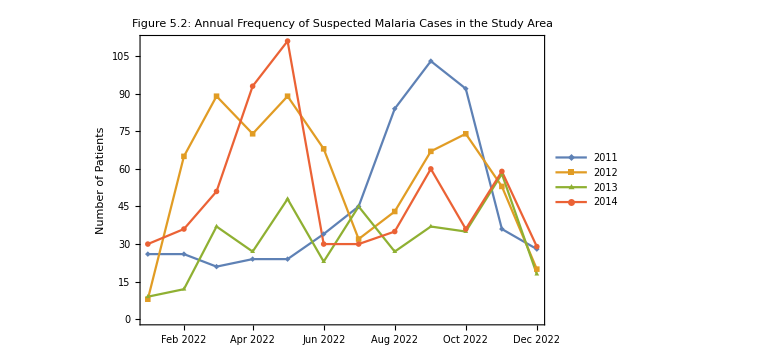

```mathematica
freq:=MapThread[{#1,#2,Splice[#3]}&,{(*Year*){"2011","2012","2013","2014"},{543,682,376,600},{{26,26,21,24,24,34,45,84,103,92,36,28},{8,65,89,74,89,68,32,43,67,74,53,20},{9,12,37,27,48,23,45,27,37,35,58,18},{30,36,51,93,111,30,30,35,60,36,59,29}}}]

patientfreq:=(freq//Map[ReplacePart[2->Nothing]/*(Apply[#1->{##2}&])])//Apply[Association]

patientsPerMonth:=KeyValueMap[Thread[{Map[DateObject/*(#["MonthName"]&)]@Thread[{ToExpression[#1],Range[12]}],#2}]&,patientfreq]

DateListPlot[patientsPerMonth,PlotLegends->{"2011","2012","2013","2014"},PlotMarkers->{{◆,10},{■,10},{▲,10},{\[MathematicaIcon],10}},PlotLabel->Row[{Style["Figure 5.2:",Bold]," Annual Frequency of Suspected Malaria Cases in the Study Area"}],Frame->{{True,False},{True,False}},FrameLabel->{"","Number of Patients"},Joined->True,ImageSize->Large]
```

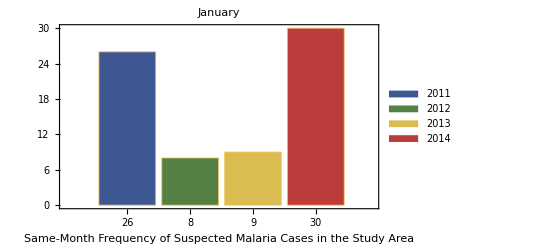
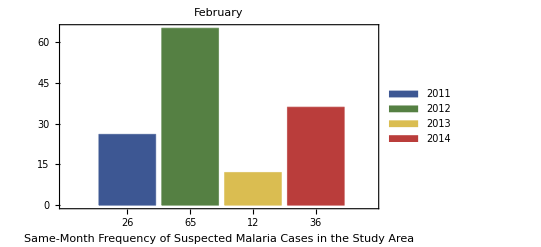
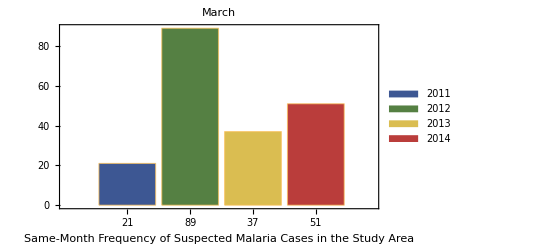
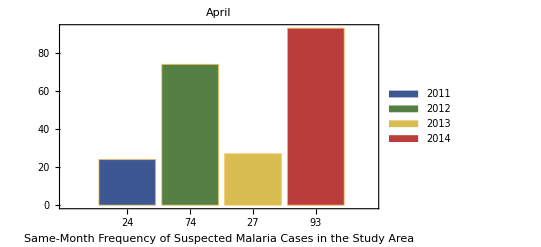
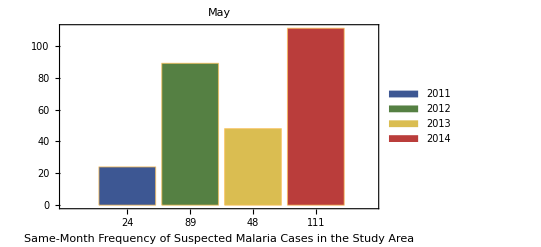
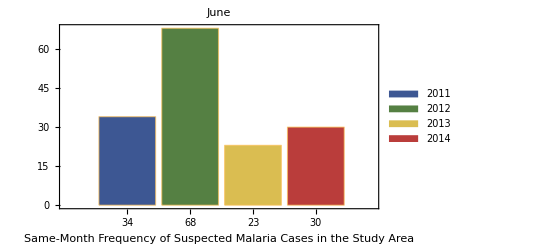
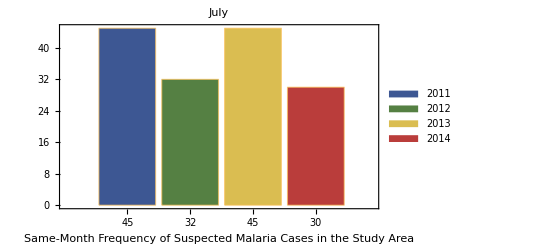
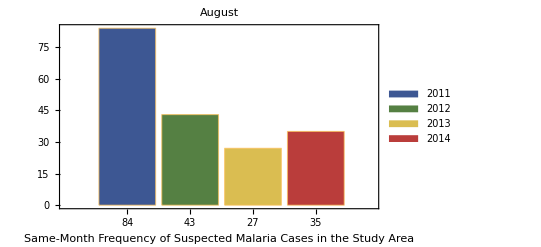

```mathematica
Table[BarChart[Labeled[#,#]&/@Table[patientsPerMonth[[All,index]][[All,2]][[n]],{n,4}],PlotLabel->patientsPerMonth[[All,index]][[All,1]][[1]],ChartStyle->"DarkRainbow",ChartLegends->{"2011","2012","2013","2014"},FrameLabel->{"Same-Month Frequency
of Suspected Malaria Cases
in the Study Area"},Frame->True],{index,1,12}]
```